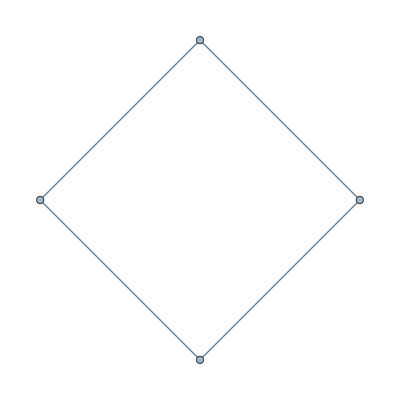

```mathematica
four=CycleGraph[4]
```

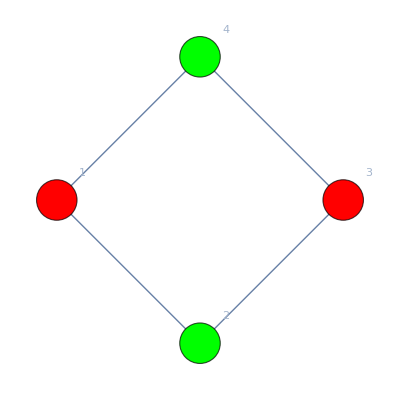
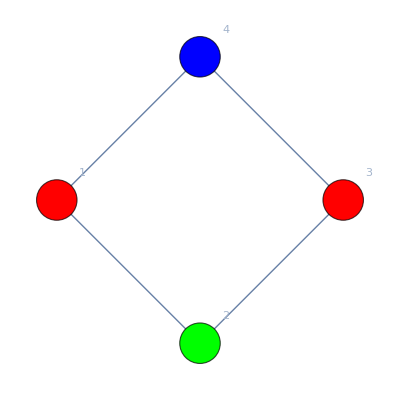
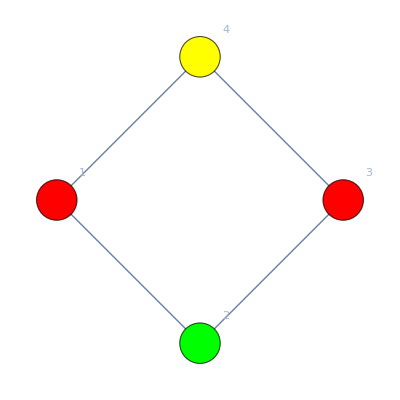
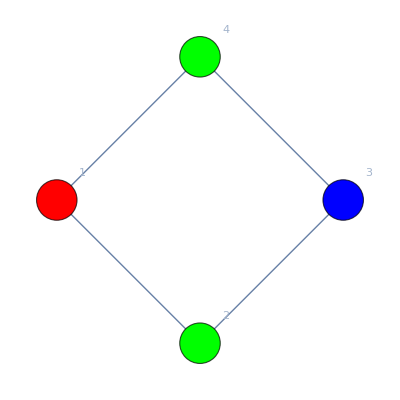
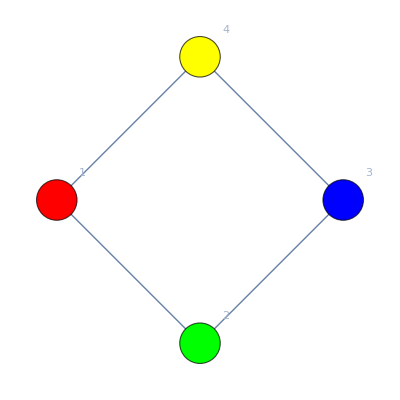
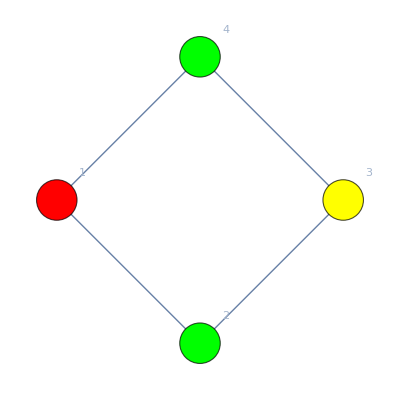
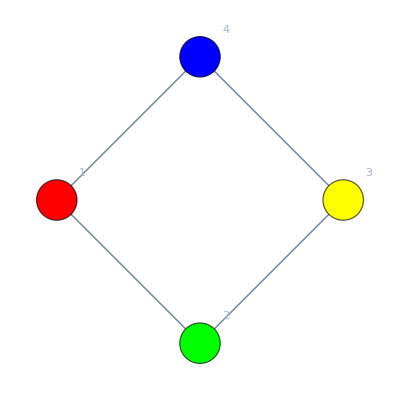

```mathematica
PaintGraph2[four,"x1==1&&x2==2",GraphLayout->"CircularEmbedding", VertexLabels->"Name"]
```

```mathematica
Subsets[VertexList[four]]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

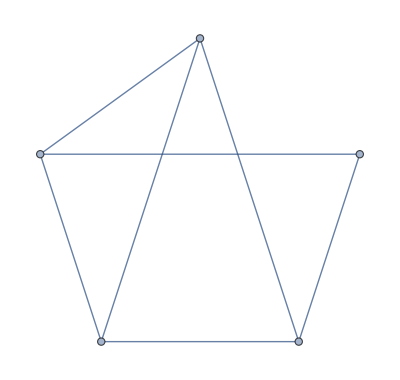

```mathematica
AddBetween[VertexAdd[four,5],5,{1,2,3}]
```

```mathematica
Most[Subsets[VertexList[four]]]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4}}

```mathematica
AddBetween[g_,from_,toList_]:=Block[{edges},
edges=Map[from<->#&,toList];
EdgeAdd[g,edges]
]
```

```mathematica
AddIfNotIsomorphic[list_,g_]:=Block[{k},
For[k=1,k≤Length[list],k++,
If[IsomorphicGraphQ[g,list[[k]]],
Return[list]
]
];
Append[list,g]
]
```

```mathematica
ComputeWouter[four_]:=Block[{g=four, all=Rest[Subsets[VertexList[four]]], max=1+VertexCount[four], i, j, k, result, complete={}, length},
length=Length[all];
Monitor[
For[i=1,i≤length,i++,
For[j=1,j≤length,j++,
For[k=1,k≤length,k++,
result=VertexAdd[g,Range[max,max+2]];
result=EdgeAdd[g,{max<->max+1,max+1<->max+2,max+2<->max}];
result=AddBetween[result,max, all[[i]]];
result=AddBetween[result,max+1, all[[j]]];
If[!PlanarGraphQ[result],Break[]];
result=AddBetween[result,max+2, all[[k]]];
If[!PlanarGraphQ[result],Break[]];
complete=AddIfNotIsomorphic[complete,Graph[result,PlotLabel->ToString[all[[i]]]<>"-"<>ToString[all[[j]]]<>"-"<>ToString[all[[k]]]]]
];
];
]
,{i,j,k,length}
];
complete
]
```

```mathematica
PlotLabel->ToString[(ChromaticPolynomial[Graph[#],4]/24)]<>"-"<>ToString[(ChromaticPolynomial[g,4]/24)]
```

```mathematica
With[
{g=CycleGraph[5]},Map[Graph[#,GraphLayout->"PlanarEmbedding", VertexLabels->"Name",GraphHighlight->EdgeList[g],GraphHighlightStyle->"Dashed" ]&,ComputeWouter[g]]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}